```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]]
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3+ⅈ (y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3)

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
imaginary = (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7);
real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
FullSimplify[real+ⅈ imaginary - map3[x,y,μ]]
```

0

```mathematica
imaginary /. x-> 1/2
```

0

```mathematica
FullSimplify[imaginary]
```

-(-1+2 x) y μ^3 (1+2 (-1+x) x μ-2 y^2 μ) (1+2 μ^2 ((-1+x) x-y^2+((-1+x)^2 x^2+(-1-6 (-1+x) x) y^2+y^4) μ))

```mathematica
im1=FullSimplify[Normal[Series[imaginary,{y,0,1}]]]
re1=Normal[Series[real,{y,0,1}]]
```

-(-1+2 x) y μ^3 (1+2 (-1+x) x μ (1+μ+3 (-1+x) x μ^2+2 (-1+x)^2 x^2 μ^3))

x μ^3-x^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7

```mathematica
im1/.x-> 1/2
re1/.x-> 1/2
```

0

μ^3/4-μ^4/16-μ^5/16+μ^6/32-μ^7/256

```mathematica
mat = {{D[real,x],D[real,y]},{D[imaginary,x],D[imaginary,y]}};
mat2 ={{D[D[real,x],x],D[D[real,y],y]},{D[D[imaginary,x],x],D[D[imaginary,y],y]}};
```

```mathematica
autovj = Eigenvalues[mat];
autovh = Eigenvalues[mat2];
eigenvecj = Eigensystem[mat];
eigenvech = Eigensystem[mat2]
```

{{0,2 μ^3 (-1-μ+6 x μ-6 x^2 μ-6 y μ+12 x y μ+6 y^2 μ-μ^2+6 x μ^2-6 x^2 μ^2-6 y μ^2+12 x y μ^2+6 y^2 μ^2+6 x μ^3-36 x^2 μ^3+60 x^3 μ^3-30 x^4 μ^3-6 y μ^3+72 x y μ^3-180 x^2 y μ^3+120 x^3 y μ^3+36 y^2 μ^3-180 x y^2 μ^3+180 x^2 y^2 μ^3+60 y^3 μ^3-120 x y^3 μ^3-30 y^4 μ^3-6 x^2 μ^4+40 x^3 μ^4-90 x^4 μ^4+84 x^5 μ^4-28 x^6 μ^4+12 x y μ^4-120 x^2 y μ^4+360 x^3 y μ^4-420 x^4 y μ^4+168 x^5 y μ^4+6 y^2 μ^4-120 x y^2 μ^4+540 x^2 y^2 μ^4-840 x^3 y^2 μ^4+420 x^4 y^2 μ^4+40 y^3 μ^4-360 x y^3 μ^4+840 x^2 y^3 μ^4-560 x^3 y^3 μ^4-90 y^4 μ^4+420 x y^4 μ^4-420 x^2 y^4 μ^4-84 y^5 μ^4+168 x y^5 μ^4+28 y^6 μ^4)},{{1,1},{-((-1-μ+6 x μ-6 x^2 μ+6 y^2 μ-μ^2+6 x μ^2-6 x^2 μ^2+6 y^2 μ^2+6 x μ^3-36 x^2 μ^3+60 x^3 μ^3-30 x^4 μ^3+36 y^2 μ^3-180 x y^2 μ^3+180 x^2 y^2 μ^3-30 y^4 μ^3-6 x^2 μ^4+40 x^3 μ^4-90 x^4 μ^4+84 x^5 μ^4-28 x^6 μ^4+6 y^2 μ^4-120 x y^2 μ^4+540 x^2 y^2 μ^4-840 x^3 y^2 μ^4+420 x^4 y^2 μ^4-90 y^4 μ^4+420 x y^4 μ^4-420 x^2 y^4 μ^4+28 y^6 μ^4)/(2 (-1+2 x) y μ (3+3 μ+3 μ^2-30 x μ^2+30 x^2 μ^2-30 y^2 μ^2-6 x μ^3+48 x^2 μ^3-84 x^3 μ^3+42 x^4 μ^3-20 y^2 μ^3+140 x y^2 μ^3-140 x^2 y^2 μ^3+42 y^4 μ^3))),1}}}

```mathematica
n=8;
L={};
For[i=38 300.,i≤ 384 30,i++,
μ=i/3000.;
For[j=1,j<10,j++,
x0=RandomReal[];
y0=RandomReal[] 10^-1;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,-y0}}];
L=Append[L,{μ,1. 10^-n Round[tab1⟦1,2⟧10^n],1. 10^-n Round[tab1⟦2,2⟧10^n]}];
]
]
L = DeleteDuplicates[L];
Clear[μ]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPointPlot3D[L,ViewPoint->{0,0,Infinity},AxesLabel->{μ,x,y}];
ListPointPlot3D[L,AxesLabel->{μ,x,y}]
```

-Graphics3D-

```mathematica
tab1=FindRoot[{Re[map3[x,y,3.80]]== x,Im[map3[x,y,3.80]]== y},{{x,0.7},{y,0.1}}];
tab1⟦2,2⟧;
Round[tab1⟦2,2⟧10^8] 10^-8;
```

```mathematica
Lnum = {}
For[i=1,i<Length[L],i++,
AppendTo[Lnum,{L⟦i⟧,i}];]
(*AppendTo[Lnum⟦i⟧,i]]*)
```

{}

```mathematica
Length[Lnum]
Length[L]
```

719

720

```mathematica
Lnum⟦720⟧
```

Part::partw: Part 720 of {{{3.8,0.514756,0.0412407},1},{{3.8,0.514756,-0.0412407},2},{{3.8,0.955636,-0.0046251},3},{{3.8,0.955636,0.0046251},4},«43»,{{3.80233,0.161083,-0.0153263},48},{{3.80233,0.514723,0.0395012},49},{{3.80233,0.514723,-0.0395012},50},«669»} does not exist.

```mathematica
afterw = Select[L,#⟦1⟧>3.8284 &];
beforew= Select[L, #⟦1⟧<3.8284 &];
```

```mathematica
ListPointPlot3D[beforew];
```

```mathematica
pontos = L;
groupA = Select[pontos, #⟦2⟧<0.1 &];
groupBstep = Select[pontos, #⟦2⟧>0.1 &];
groupB = Select[groupBstep, #⟦2⟧<0.2 &];
groupCstep = Select[pontos, #⟦2⟧>0.4 &];
groupC= Select[groupCstep, #⟦2⟧<0.6 &];
groupDstep = Select[pontos, #⟦2⟧>0.6 &];
groupD = Select[groupDstep, #⟦2⟧<0.8 &];
groupE = Select[pontos, #⟦2⟧>0.8 &];
```

```mathematica
ListPointPlot3D[groupE]
```

-Graphics3D-

```mathematica
groups1 = {groupB, groupC, groupE};
groups2 = {groupA, groupD};

thelistp = {{},{},{}};
thelistf = {{},{},{}};
thelistf2 = {{},{}};
```

thelistf -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 8 termos:  {gp1xf, gp1yf, gp2xf, gp2yf, ... }, sendo cada termo uma função interpolada de μ com relação a x ou y de cada ramo de um grupo (B1, B2, B3, B4).

thelistp -> lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverão 4 termos:  {gp1, gp2, gp3, gp4 }, sendo cada termo uma lista contendo {μ, x, y} referentes a cada ramo de um grupo  (B1, B2, B3, B4).

```mathematica
For[i=1,i≤ Length[groups1],i++,
before = Select[groups1⟦i⟧,#⟦1⟧≤ 3.8284 &];
after = Select[groups1⟦i⟧, #⟦1⟧>3.8284 &];
gp1 = Select[before, #⟦3⟧≥ 0 &];
gp3 = Select[before, #⟦3⟧<0 &];
gp2 = Select[after,#⟦2⟧≥ before⟦Length[before],2⟧ &];
gp4 = Select[after,#⟦2⟧<before⟦Length[before],2⟧ &];
(* step com drop adicionado*)
gp1x = DeleteDuplicates[Drop[gp1,0,{3}]];
gp1y = DeleteDuplicates[Drop[gp1,0,{2}]];
gp2x = DeleteDuplicates[Drop[gp2,0,{3}]];
gp2y = DeleteDuplicates[Drop[gp2,0,{2}]];
gp3x = DeleteDuplicates[Drop[gp3,0,{3}]];
gp3y =DeleteDuplicates[Drop[gp3,0,{2}]];
gp4x = DeleteDuplicates[Drop[gp4,0,{3}]];
gp4y =DeleteDuplicates[Drop[gp4,0,{2}]];
gp1xf = Interpolation[gp1x];
gp1yf = Interpolation[gp1y];
gp2xf = Interpolation[gp2x];
gp2yf = Interpolation[gp2y];
gp3xf = Interpolation[gp3x];
gp3yf = Interpolation[gp3y];
gp4xf = Interpolation[gp4x];
gp4yf = Interpolation[gp4y];
AppendTo[thelistp⟦i⟧,gp1] ;
AppendTo[thelistp⟦i⟧,gp2];
AppendTo[thelistp⟦i⟧,gp3];
AppendTo[thelistp⟦i⟧,gp4];
AppendTo[thelistf⟦i⟧,gp1xf];
AppendTo[thelistf⟦i⟧,gp1yf];
AppendTo[thelistf⟦i⟧,gp2xf];
AppendTo[thelistf⟦i⟧,gp2yf];
AppendTo[thelistf⟦i⟧,gp3xf];
AppendTo[thelistf⟦i⟧,gp3yf];
AppendTo[thelistf⟦i⟧,gp4xf];
AppendTo[thelistf⟦i⟧,gp4yf];]
```

thelistf2 -->  lista contendo uma sublista para cada “grupo” contido na lista groups2.  Para cada sublista haverão 4 termos:  {gp1xf, gp1yf, gp2xf, gp2yf}, sendo cada termo uma função interpolada de μ com relação a x ou y de cada ramo de um grupo (A1, A2).

```mathematica
For[i=1,i≤ Length[groups2],i++,
gpp1 = Select[groups2⟦i⟧,#⟦1⟧≤ 3.8284 &];
gpp2 = Select[groups2⟦i⟧, #⟦1⟧>3.8284 &];
gpp1x = DeleteDuplicates[Drop[gpp1,0,{3}]];
gpp1y = DeleteDuplicates[Drop[gpp1,0,{2}]];
gpp2x = DeleteDuplicates[Drop[gpp2,0,{3}]];
gpp2y = DeleteDuplicates[Drop[gpp2,0,{2}]];
gpp1xf = Interpolation[gpp1x];
gpp1yf = Interpolation[gpp1y];
gpp2xf = Interpolation[gpp2x];
gpp2yf = Interpolation[gpp2y];
AppendTo[thelistf2⟦i⟧,gpp1xf];
AppendTo[thelistf2⟦i⟧,gpp1yf];
AppendTo[thelistf2⟦i⟧,gpp2xf];
AppendTo[thelistf2⟦i⟧,gpp2yf];]
```

```mathematica
gpp1⟦1⟧
```

{3.8,0.736842,0.}

```mathematica
thelistf2⟦2⟧
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

autovjlist -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverá 4 termos:  {autovj1, autovj2, ...}, sendo cada termo uma função interpolada de μ com relação a seu autovalor de cada ramo de um grupo (B1, B2, B3, B4) da matriz jacobiana.

autovhlist -->  lista contendo uma sublista para cada “grupo” contido na lista groups.  Para cada sublista haverá 4 termos:  {autovh1, autovh2, ...}, sendo cada termo uma função interpolada de μ com relação a seu autovalor de cada ramo de um grupo (B1, B2, B3, B4) da matriz hessiana.

```mathematica
Clear[autovjlist]
```

```mathematica
autovjlist = {};
autovhlist = {};
For[i=1,i≤ Length[groups1],i++,
autovj1 [μ_]= autovj/.{x-> thelistf⟦i,1⟧[μ],y-> thelistf⟦i,2⟧[μ]};
autovj2 [μ_]= autovj/.{x-> thelistf⟦i,3⟧[μ],y-> thelistf⟦i,4⟧[μ]};
autovj3 [μ_]= autovj/.{x-> thelistf⟦i,5⟧[μ],y-> thelistf⟦i,6⟧[μ]};
autovj4 [μ_]= autovj/.{x-> thelistf⟦i,7⟧[μ],y-> thelistf⟦i,8⟧[μ]};
autovjgroup = {autovj1[μ], autovj2[μ], autovj3[μ], autovj4[μ]};
AppendTo[autovjlist, autovjgroup];
autovh1 [μ_]= autovh/.{x-> thelistf⟦i,1⟧[μ],y-> thelistf⟦i,2⟧[μ]};
autovh2 [μ_]= autovh/.{x-> thelistf⟦i,3⟧[μ],y-> thelistf⟦i,4⟧[μ]};
autovh3 [μ_]= autovh/.{x-> thelistf⟦i,5⟧[μ],y-> thelistf⟦i,6⟧[μ]};
autovh4 [μ_]= autovh/.{x-> thelistf⟦i,7⟧[μ],y-> thelistf⟦i,8⟧[μ]};
autovhgroup = {autovh1[μ], autovh2[μ], autovh3[μ], autovh4[μ]};
AppendTo[autovhlist, autovhgroup]]
```

```mathematica
autovjlist2 = {};
autovhlist2 = {};
For[i=1,i≤ Length[groups2],i++,
autovj1 [μ_]= autovj/.{x-> thelistf2⟦i,1⟧[μ],y-> thelistf2⟦i,2⟧[μ]};
autovj2 [μ_]= autovj/.{x-> thelistf2⟦i,3⟧[μ],y-> thelistf2⟦i,4⟧[μ]};
autovjgroup = {autovj1[μ], autovj2[μ]};
AppendTo[autovjlist2, autovjgroup];
autovh1 [μ_]= autovh/.{x-> thelistf2⟦i,1⟧[μ],y-> thelistf2⟦i,2⟧[μ]};
autovh2 [μ_]= autovh/.{x-> thelistf2⟦i,3⟧[μ],y-> thelistf2⟦i,4⟧[μ]};
autovhgroup = {autovh1[μ], autovh2[μ]};
AppendTo[autovhlist2, autovhgroup]]
```

```mathematica
autovjlist⟦1,1,1⟧/. μ-> 3.8
```

1.16-2.736 ⅈ

```mathematica
autovjlist⟦1,2,1⟧/. μ-> 3.8
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

8.68413×10^12

```mathematica
autovjlist⟦1,3,1⟧/. μ-> 3.8
```

1.16-2.736 ⅈ

```mathematica
autovjlist⟦1,4,1⟧/. μ-> 3.8
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-3.28251×10^9

0

0

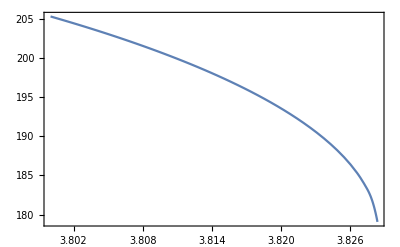

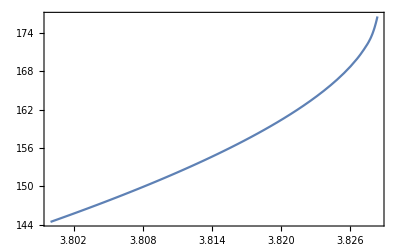

```mathematica
autovhlist⟦1,1,1⟧/. μ-> 3.8
autovhlist⟦1,3,1⟧/. μ-> 3.8
teste=autovhlist⟦1,1,2⟧;
Plot[teste,{μ,3.8,3.8284},Frame->True]
teste=autovhlist⟦1,3,2⟧;
Plot[teste,{μ,3.8,3.8284},Frame->True]
```

0

0

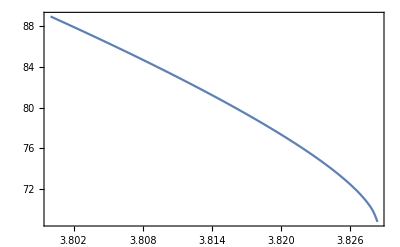

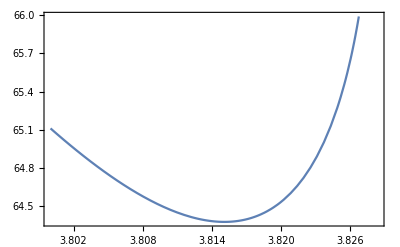

```mathematica
autovhlist⟦2,1,1⟧/. μ-> 3.8
autovhlist⟦2,3,1⟧/. μ-> 3.8
teste=autovhlist⟦2,1,2⟧;
Plot[teste,{μ,3.8,3.8284},Frame->True]
teste=autovhlist⟦2,3,2⟧;
Plot[teste,{μ,3.8,3.8284},Frame->True]
```

0

0

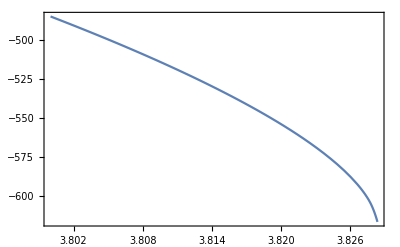

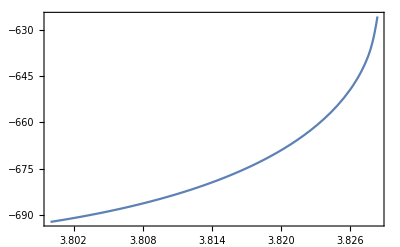

```mathematica
autovhlist⟦3,1,1⟧/. μ-> 3.8
autovhlist⟦3,3,1⟧/. μ-> 3.8
teste=autovhlist⟦3,1,2⟧;
Plot[teste,{μ,3.8,3.8284},Frame->True]
teste=autovhlist⟦3,3,2⟧;
Plot[teste,{μ,3.8,3.8284},Frame->True]
```

Abaixo, comportamento que indica que o grupo E possui pouca contribuição (...), porque o inverso da frequência (...) ----> buscar entender melhor <-----

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

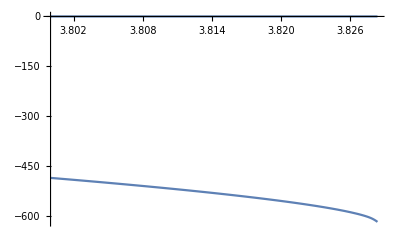

```mathematica
Plot[{autovhlist⟦3,1⟧,1.1autovhlist⟦3,3⟧},{μ,3.8,3.8284}]
```

Código com a mesma funcionalidade de autovjlist para testar o funcionamento de forma separada de cada elemento que estaria contido na lista.
Em seguida, um plot dos autovalores em função de μ para os 4 autovj’s.

```mathematica
autovj1 [μ_]= autovj/.{x-> thelistf⟦1,1⟧[μ],y-> thelistf⟦1,2⟧[μ]};
autovj2 [μ_]= autovj/.{x-> thelistf⟦1,3⟧[μ],y-> thelistf⟦1,4⟧[μ]};
autovj4 [μ_]= autovj/.{x-> thelistf⟦1,7⟧[μ],y-> thelistf⟦1,8⟧[μ]};
autovj3 [μ_]= autovj/.{x-> thelistf⟦1,5⟧[μ],y-> thelistf⟦1,6⟧[μ]};
```

```mathematica
autovj1[3.81]
```

{1.1039-2.22286 ⅈ,1.1039+2.22286 ⅈ}

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

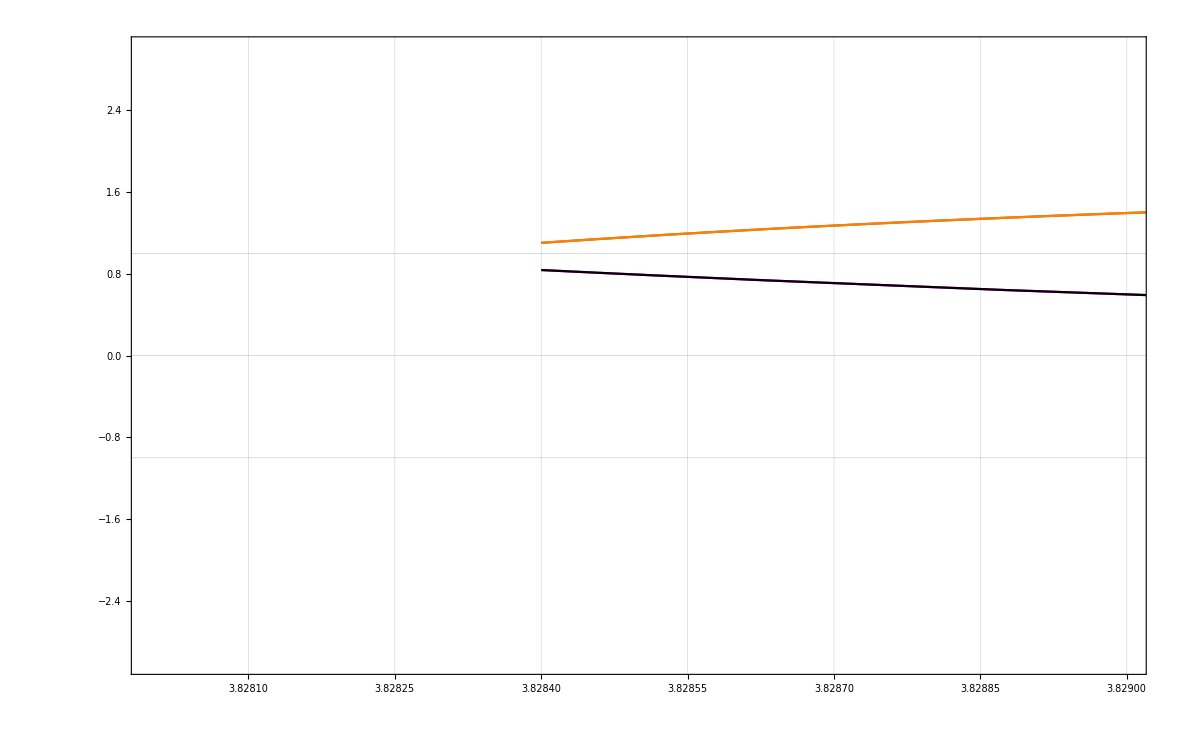

```mathematica
Show[
Plot[autovj1[μ]⟦1⟧,{μ,3.82,3.8284},PlotRange->{{3.828,3.829},{-3,3}},PlotStyle->Blue,Frame->True,GridLines->{Automatic, {-1,0,1}}],Plot[autovj1[μ]⟦2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->Red],
Plot[autovj2[μ]⟦1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Brown],
Plot[autovj2[μ]⟦2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Orange],
Plot[autovj3[μ]⟦1⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Green,Dashed}],
Plot[autovj3[μ]⟦2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Yellow,Dashed}],
Plot[autovj4[μ]⟦1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Magenta],
Plot[autovj4[μ]⟦2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Black]
]
```

Tentativas de calcular uma média ponderada dos autovalores da Hessiana.

```mathematica
xyz[μ_]= (thelistf⟦1,1⟧[μ])/Abs[autovhlist⟦1,1,2⟧]+(thelistf⟦1,5⟧[μ])/Abs[autovhlist⟦1,3,2⟧]+(thelistf⟦2,1⟧[μ])/Abs[autovhlist⟦2,1,2⟧]+(thelistf⟦2,5⟧[μ])/Abs[autovhlist⟦2,3,2⟧]+(thelistf⟦3,1⟧[μ])/Abs[autovhlist⟦3,1,2⟧]+(thelistf⟦3,5⟧[μ])/Abs[autovhlist⟦3,3,2⟧]+(thelistf2⟦1,1⟧[μ])/Abs[autovhlist2⟦1,1,2⟧]+(thelistf2⟦2,1⟧[μ])/Abs[autovhlist2⟦2,1,2⟧];
```

```mathematica
Abs[autovhlist2⟦2,1,1⟧]/.μ-> 3.82
```

0

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

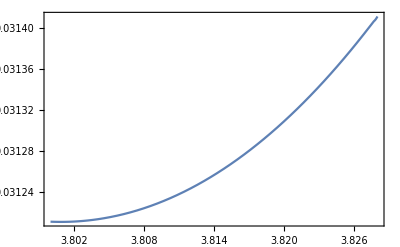

```mathematica
Plot[xyz[μ],{μ,3.8,3.828},Frame->True]
```

```mathematica
media[μ_]= thelistf⟦1,1⟧[μ]+thelistf⟦1,3⟧[μ]+thelistf⟦2,1⟧[μ]+thelistf⟦2,3⟧[μ]+thelistf⟦3,1⟧[μ]+thelistf⟦3,3⟧[μ]+thelistf2⟦1,1⟧[μ]+thelistf2⟦2,1⟧[μ];
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

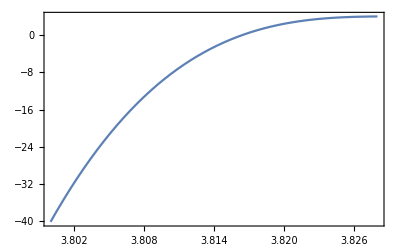

```mathematica
Plot[media[μ],{μ,3.8,3.828},Frame->True]
```

```mathematica
Length[thelistf⟦1⟧]
```

8

```mathematica
Length[autovhlist⟦1⟧]
```

4

```mathematica
autovhlist⟦1,1,2⟧/.μ-> 3.8
```

205.304

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

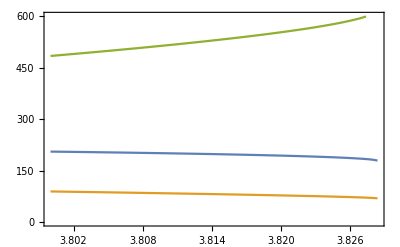

```mathematica
Plot[{autovhlist⟦1,1,2⟧,autovhlist⟦2,1,2⟧,-autovhlist⟦3,1,2⟧} ,{μ,3.8,3.8284},PlotRange->{0,600},Frame->True]
```

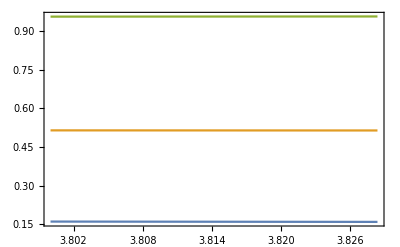

```mathematica
Plot[{thelistf⟦1,1⟧[μ],thelistf⟦2,1⟧[μ], thelistf⟦3,1⟧[μ]},{μ,3.8,3.8284},Frame->True]
```

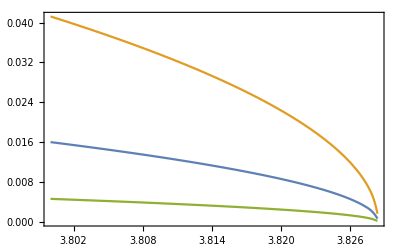

```mathematica
Plot[{thelistf⟦1,2⟧[μ],thelistf⟦2,2⟧[μ], thelistf⟦3,2⟧[μ]},{μ,3.8,3.8284},Frame->True]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

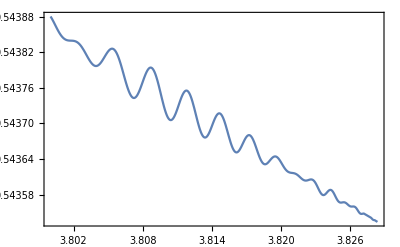

```mathematica
Plot[(thelistf⟦1,1⟧[μ]+thelistf⟦2,1⟧[μ]+thelistf⟦3,1⟧[μ])/3+ 2 10^-3(3.8284-μ)Cos[(autovhlist⟦1,1,2⟧+autovhlist⟦2,1,2⟧)/2 μ]Cos[(autovhlist⟦1,1,2⟧-autovhlist⟦2,1,2⟧)/2 μ],{μ,3.8,3.8284},Frame->True]
```

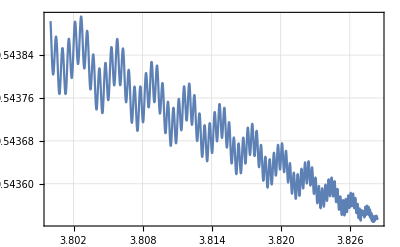

```mathematica
teste1=autovhlist⟦1,1,2⟧;
teste2=autovhlist⟦2,1,2⟧;
teste3=autovhlist⟦3,1,2⟧;
Plot[(thelistf⟦1,1⟧[μ]+thelistf⟦2,1⟧[μ]+thelistf⟦3,1⟧[μ])/3+ 10^-5 thelistf⟦1,2⟧[μ]Cos[teste1 μ]+ 10^-3 thelistf⟦2,2⟧[μ]Cos[teste2 μ]+ 10^-2 thelistf⟦3,2⟧[μ]Cos[teste3  μ],{μ,3.8,3.8284},Frame->True,GridLines->Automatic]
```

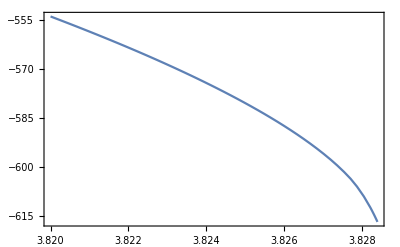

```mathematica
teste=autovhlist⟦3,1,2⟧;
Plot[teste,{μ,3.82,3.8284},Frame->True]
```

```mathematica
x = 0.1;
listpoints = {};
For[μ = 3.8, μ<3.835,μ=μ+0.0001,
(*For[i=1,i<100,i++,
x = μ x(1-x)
];*)
AppendTo[listpoints,{μ,x}];
For[i=1,i<100,i++,
x =μ x(1-x);
AppendTo[listpoints,{μ,x}];
]
]
```

```mathematica
x = 0.5;
listpointsx = {};
μ = 3.8;
AppendTo[listpointsx,x];
For[i=1,i<100,i++,
x =μ x(1-x);
AppendTo[listpointsx,x];
]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

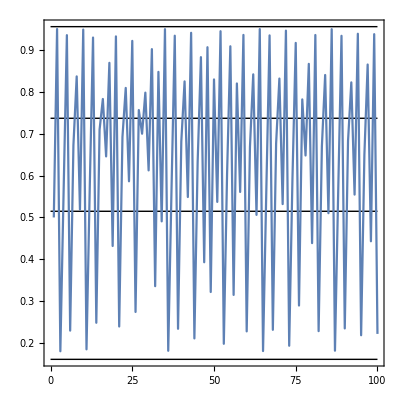

```mathematica
Show[Graphics[Line[{{0,thelistf⟦1,1⟧[3.8]},{100,thelistf⟦1,1⟧[3.8]}}]],
Graphics[Line[{{0,thelistf⟦2,1⟧[3.8]},{100,thelistf⟦2,1⟧[3.8]}}]],
Graphics[Line[{{0,thelistf⟦3,1⟧[3.8]},{100,thelistf⟦3,1⟧[3.8]}}]],
Graphics[Line[{{0,thelistf2⟦2,1⟧[3.8]},{100,thelistf2⟦2,1⟧[3.8]}}]],
ListPlot[listpointsx,PlotStyle->PointSize[0.005],Frame->True, Joined-> True],PlotRange-> All,Frame-> True,  AspectRatio-> 1]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

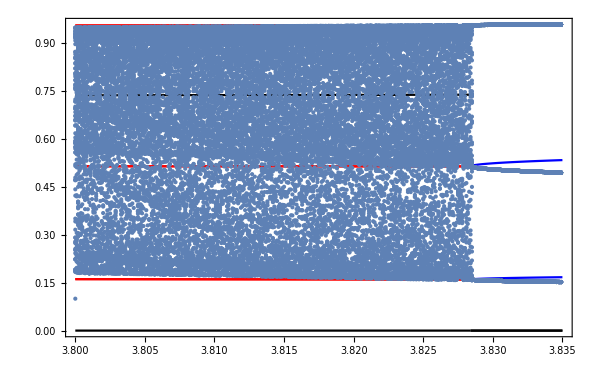

```mathematica
Show[Plot[{thelistf⟦1,1⟧[μ],thelistf⟦1,5⟧[μ],thelistf⟦2,1⟧[μ],thelistf⟦2,5⟧[μ],thelistf⟦3,1⟧[μ],thelistf⟦3,5⟧[μ]},{μ,3.8,3.8284},PlotStyle->Red],
Plot[{thelistf2⟦1,1⟧[μ],thelistf2⟦2,1⟧[μ]},{μ,3.8,3.8284},PlotStyle->Black],
Plot[{thelistf⟦1,3⟧[μ],thelistf⟦1,7⟧[μ],thelistf⟦2,3⟧[μ],thelistf⟦2,7⟧[μ],thelistf⟦3,3⟧[μ],thelistf⟦3,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Blue],
Plot[{thelistf2⟦1,2⟧[μ],thelistf2⟦2,2⟧[μ]},{μ,3.8284, 3.835},PlotStyle->Black],
ListPlot[listpoints,PlotStyle->PointSize[0.005],Frame->True],PlotRange-> All,Frame-> True]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

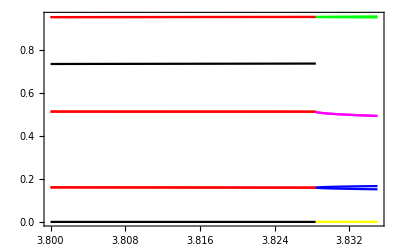

```mathematica
Show[Plot[{thelistf⟦1,1⟧[μ],thelistf⟦1,5⟧[μ],thelistf⟦2,1⟧[μ],thelistf⟦2,5⟧[μ],thelistf⟦3,1⟧[μ],thelistf⟦3,5⟧[μ]},{μ,3.8,3.8284},PlotStyle->Red],
Plot[{thelistf2⟦1,1⟧[μ],thelistf2⟦2,1⟧[μ]},{μ,3.8,3.8284},PlotStyle->Black],
Plot[{thelistf⟦1,3⟧[μ],thelistf⟦1,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Blue],
Plot[{thelistf⟦2,7⟧[μ],thelistf⟦2,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Magenta],
Plot[{thelistf⟦3,3⟧[μ],thelistf⟦3,7⟧[μ]},{μ,3.8284,3.835},PlotStyle->Green],
Plot[{thelistf2⟦1,2⟧[μ],thelistf2⟦2,2⟧[μ]},{μ,3.8284, 3.835},PlotStyle->Yellow],
PlotRange-> All,Frame-> True]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Part::partd: Part specification Plot[autovjlist]⟦1,1,1⟧ is longer than depth of object.

InterpolatingFunction::dmval: Input value {3.82} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

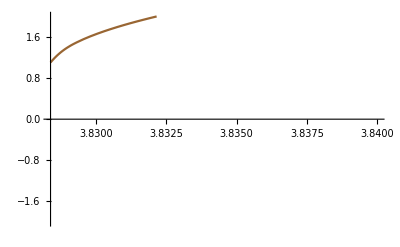
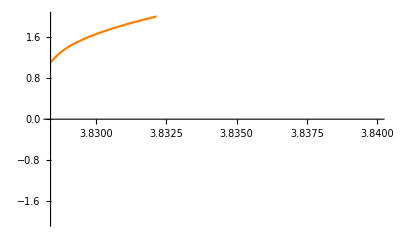
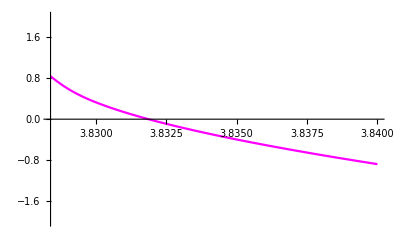
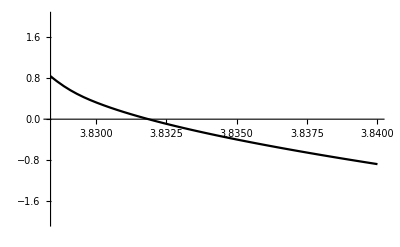
Show[Plot[autovjlist]⟦1,1,1⟧,{3.8,3.82,3.8284},PlotRange→{{3.828,3.829},{-3,3}},PlotStyle→RGBColor[0, 0, 1],Frame→True,GridLines→{Automatic,{-1,0,1}},-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
Show[Plot[autovjlist]⟦1,1,1⟧,{μ,3.82,3.8284},PlotRange->{{3.828,3.829},{-3,3}},PlotStyle->Blue,Frame->True,GridLines->{Automatic, {-1,0,1}},Plot[autovjlist⟦1,1,2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->Red],
Plot[autovjlist⟦1,2,1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Brown],
Plot[autovjlist⟦1,2,2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Orange],
Plot[autovjlist⟦1,3,1⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Green,Dashed}],
Plot[autovjlist⟦1,3,2⟧,{μ,3.82,3.8284},PlotRange->{-2,2},PlotStyle->{Yellow,Dashed}],
Plot[autovjlist⟦1,4,1⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Magenta],
Plot[autovjlist⟦1,4,2⟧,{μ,3.8284,3.84},PlotRange->{-2,2},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {3.82} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

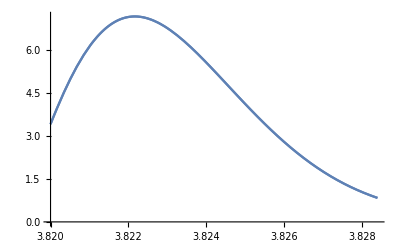

```mathematica
Plot[autovjlist⟦1,4⟧,{μ,3.82,3.8284}]
```

```mathematica
autovjlist⟦1,1⟧
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.16-2.736 ⅈ,1.16+2.736 ⅈ}

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

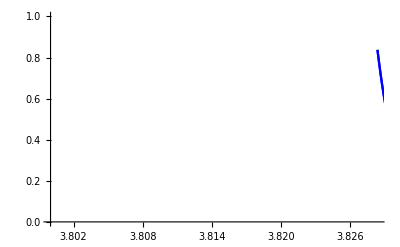

```mathematica
Show[
Plot[{autovjlist⟦1,1⟧,autovjlist⟦1,3⟧},{μ,3.8,3.8284}],
Plot[autovjlist⟦1,2⟧,{μ,3.8284,3.835},PlotStyle->Red],
Plot[autovjlist⟦1,4⟧,{μ,3.8284,3.835}, PlotStyle->Blue]]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

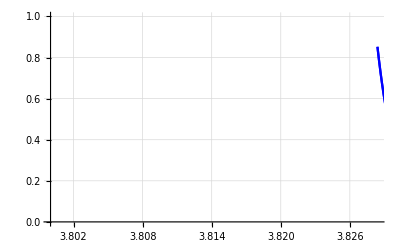

```mathematica
Show[
Plot[{autovjlist⟦2,1⟧,autovjlist⟦2,3⟧},{μ,3.8,3.8284}],
Plot[autovjlist⟦2,2⟧,{μ,3.8284,3.835},PlotStyle->Red],
Plot[autovjlist⟦2,4⟧,{μ,3.8284,3.835}, PlotStyle->Blue], GridLines-> Automatic]
```

InterpolatingFunction::dmval: Input value {3.825} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

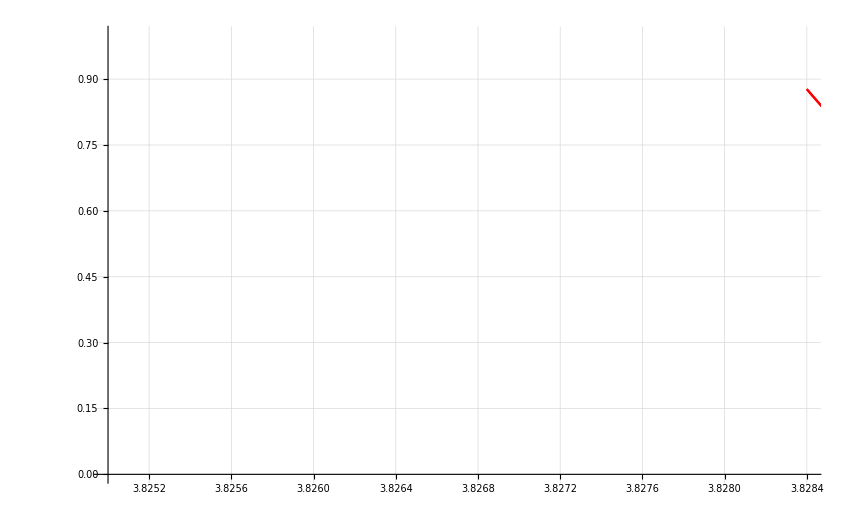

```mathematica
Show[
Plot[{autovjlist⟦3,1⟧,autovjlist⟦2,3⟧},{μ,3.825,3.8284}],
Plot[autovjlist⟦3,2⟧,{μ,3.8284,3.835},PlotStyle->Red],
Plot[autovjlist⟦3,4⟧,{μ,3.8284,3.835}, PlotStyle->Blue], GridLines-> Automatic]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

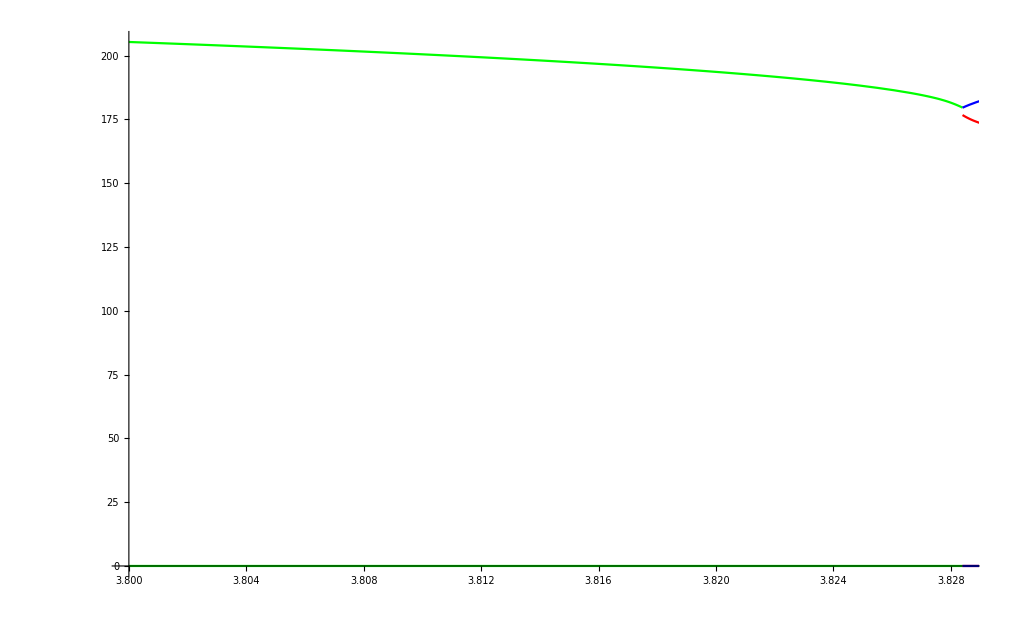

```mathematica
Show[
Plot[autovhlist⟦1,1⟧,{μ,3.8,3.8284}, PlotStyle->Green],
Plot[autovjlist⟦2,3⟧,{μ,3.8,3.8284}, PlotStyle->{Brown, Dashed}],
Plot[autovhlist⟦1,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦1,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue]]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

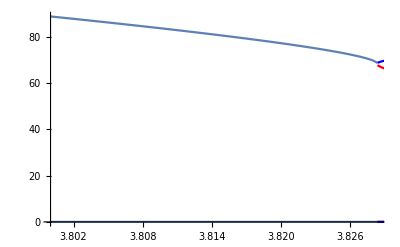

```mathematica
Show[
Plot[{autovhlist⟦2,1⟧,autovjlist⟦2,3⟧},{μ,3.8,3.8284}],
Plot[autovhlist⟦2,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦2,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue]]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

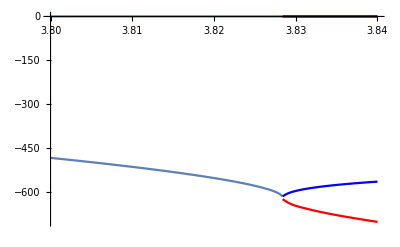

```mathematica
Show[
Plot[{autovhlist⟦3,1⟧,autovhlist⟦3,3⟧},{μ,3.8,3.8284}],
Plot[autovhlist⟦3,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦3,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue], PlotRange-> All]
```

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

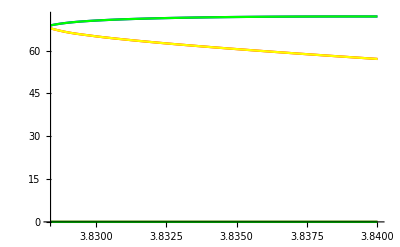

```mathematica
Show[
Plot[autovhlist⟦2,2⟧,{μ,3.8284,3.84},PlotStyle->Red],
Plot[autovhlist⟦2,4⟧,{μ,3.8284,3.84}, PlotStyle->Blue],
Plot[autovhlist⟦2,2⟧,{μ,3.8284,3.84},PlotStyle->Yellow],
Plot[autovhlist⟦2,4⟧,{μ,3.8284,3.84}, PlotStyle->Green], PlotRange-> All]
```

InterpolatingFunction::dmval: Input value {3.8284} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

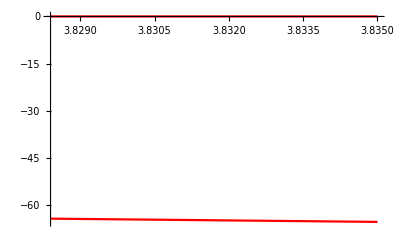

```mathematica
Plot[autovhlist2⟦2,2⟧,{μ,3.8284,3.835},PlotStyle->Red]
```

InterpolatingFunction::dmval: Input value {3.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

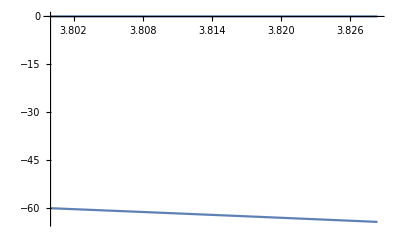

```mathematica
Plot[autovhlist2⟦2,1⟧,{μ,3.8,3.8284}]
```

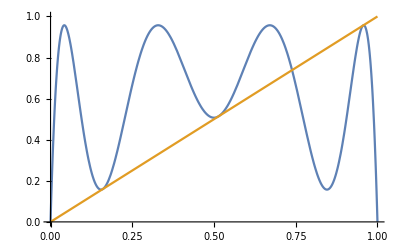

```mathematica
Plot[{map3[x,0,3.8284],x},{x,0,1}]
```

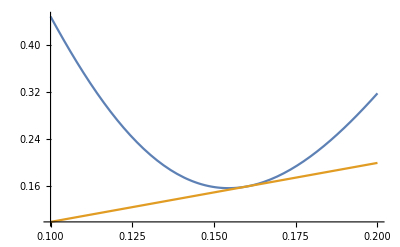

```mathematica
Plot[{map3[x,0,3.8284],x},{x,0.1,0.2}]
```

```mathematica
groupB⟦1⟧
```

{3.8,0.161187,0.016016}

```mathematica
Block[{μ = 3.8},
listpointsxy = {};

For[j=2,j<1000,j++,
x =(j-1)10^-3;
For[k=1,k≤ 1,k++,
y = k 10^-3;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
For[i=1,i<100,i++,
If[x^2+y^2≤ 1,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α  y,0}],
i=100]
]
]
];

Length[listpointsxy];

pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];
Show[Plot3D[10^-5 Re[D[map3[xx,y,μ]-xx,{xx,2}]]^2/. xx-> x,{x,0,1},{y,-0.1,0.1},PlotRange->{0,1},ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
]
```

-Graphics3D-

```mathematica
groupE⟦1,1⟧
```

3.8

8000

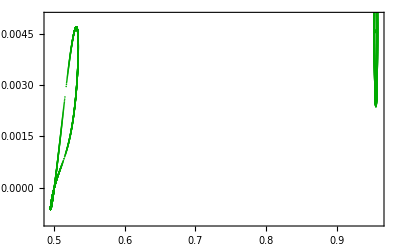

```mathematica
Block[{μ = 3.8},
list1 = {};
For[j=-1,j<1,j=j+0.001,
x=groupE⟦1,2⟧-2 10^-3 √(1-j^2)11/10;
y=groupE⟦1,3⟧+2 10^-3(j 11/10);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupE⟦1,2⟧+2 10^-3 √(1-j^2)11/10;
y=groupE⟦1,3⟧+2 10^-3(j 11/10);
AppendTo[list1,{x, y}];
For[i=1,i<2,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
]
];
Length[list1]
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange->  {-0.001,0.005}]
```

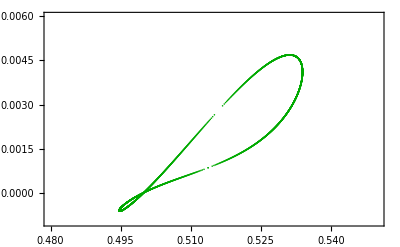

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange->  {{0.48,0.55},{-0.001,0.006}}]
```

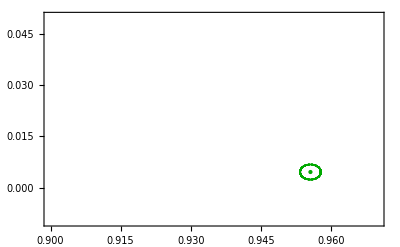

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange->  {{0.9,0.97},{-0.01,0.05}}]
```

Existe um ponto próximo de x=0.955 que é levado, por 1 iteração do mapa, a y~0 ˜˜.08!!

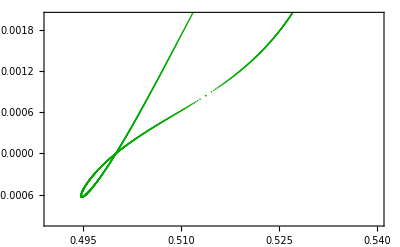

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->Darker[Green]],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.49,0.54},{-0.001,0.002}}]
```

```mathematica
map[groupE⟦1,2⟧ 0.9,groupE⟦1,3⟧,groupE⟦1,1⟧]
groupE⟦1,2⟧
groupC⟦1,2⟧
```

0.457443-0.0125033 ⅈ

0.955652

0.514756

```mathematica
imaginary/. {x-> groupE⟦1,2⟧+α,y-> groupE⟦1,3⟧,μ-> groupE⟦1,1⟧}
```

0.250023-9.64159 (0.955652+α)+110.005 (0.955652+α)^2-557.924 (0.955652+α)^3+1459.5 (0.955652+α)^4-2049.03 (0.955652+α)^5+1465.23 (0.955652+α)^6-418.637 (0.955652+α)^7

{{0.473404,0.00456803,3.80067},{0.594309,0.00456803,3.80067},{0.772079,0.00456803,3.80067},{0.940895,0.00456803,3.80067},{1.10971,0.00456803,3.80067},{1.28748,0.00456803,3.80067},{1.40839,0.00456803,3.80067},{0.0325087,0.0412407,3.8},{0.153414,0.0412407,3.8},{0.331184,0.0412407,3.8},{0.5,0.0412407,3.8},{0.668816,0.0412407,3.8},{0.846586,0.0412407,3.8},{0.967491,0.0412407,3.8},{-0.321061,0.016016,3.8},{-0.200155,0.016016,3.8},{-0.0223853,0.016016,3.8},{0.14643,0.016016,3.8},{0.315246,0.016016,3.8},{0.493016,0.016016,3.8},{0.613922,0.016016,3.8}}

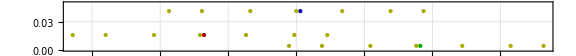

```mathematica
Clear[x,y]
subs1=NSolve[imaginary== 0/. {x-> groupE⟦1,2⟧+α,y-> groupE⟦1,3⟧,μ-> groupE⟦1,1⟧},α,Reals]⟦All,1,2⟧;
lista1=Table[{groupE⟦1,2⟧+α,groupE⟦1,3⟧,groupE⟦1,1⟧}/.α->subs⟦j⟧,{j,1,Length[subs]}];
subs2=NSolve[imaginary== 0/. {x-> groupC⟦1,2⟧+α,y-> groupC⟦1,3⟧,μ-> groupC⟦1,1⟧},α,Reals]⟦All,1,2⟧;
lista2=Table[{groupC⟦1,2⟧+α,groupC⟦1,3⟧,groupC⟦1,1⟧}/.α->subs2⟦j⟧,{j,1,Length[subs]}];
subs3=NSolve[imaginary== 0/. {x-> groupB⟦1,2⟧+α,y-> groupB⟦1,3⟧,μ-> groupB⟦1,1⟧},α,Reals]⟦All,1,2⟧;
lista3=Table[{groupB⟦1,2⟧+α,groupB⟦1,3⟧,groupB⟦1,1⟧}/.α->subs2⟦j⟧,{j,1,Length[subs]}];
lista=Join[lista1,lista2,lista3]
p1=Show[
Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Table[Graphics[{Darker[Yellow],PointSize[Medium],Point[lista⟦j,1;;2⟧]}],{j,1,Length[lista]}],PlotRange-> {0,0.05},Frame-> True,GridLines-> Automatic,AspectRatio-> 1/10,ImageSize-> Large]
```

```mathematica
groupB⟦1,3⟧
```

0.016016

9822

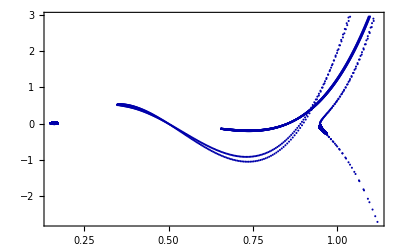

```mathematica
Block[{μ = 3.8},
list2 = {};
For[j=-1,j<1,j=j+0.001,
x=groupB⟦1,2⟧+10^-2 √(1-j^2)11/10;
y=groupB⟦1,3⟧+10^-2(j 11/10);
AppendTo[list2,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list2,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupB⟦1,2⟧-10^-2 √(1-j^2)11/10;
y=groupB⟦1,3⟧+10^-2(j 11/10);
AppendTo[list2,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list2,{x, y}],i=5]
]
]
];
Length[list2]
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],PlotRange-> All]
```

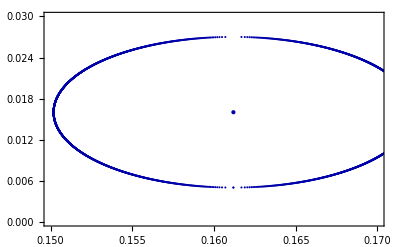

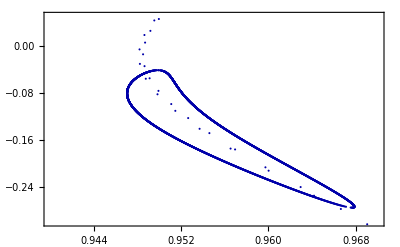

```mathematica
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],PlotRange-> {{0.15,0.17},{0,0.03}}]
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Darker[Blue]],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],PlotRange-> {{0.94,0.97},{-0.3,0.05}}]
```

13277

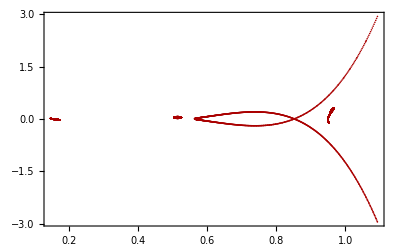

```mathematica
Block[{μ = 3.8},
list3 = {};
For[j=-1,j<1,j=j+0.001,
x=groupC⟦1,2⟧+10^-2 √(1-j^2)11/10;
y=groupC⟦1,3⟧+ 10^-2(j 11/10);
AppendTo[list3,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupC⟦1,2⟧-10^-2 √(1-j^2)11/10;
y=groupC⟦1,3⟧+10^-2(j 11/10);
AppendTo[list3,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
]
];
Length[list3]
Show[ListPlot[list3,Frame->True,Joined->False,PlotStyle->Darker[Red]],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],PlotRange-> All]
```

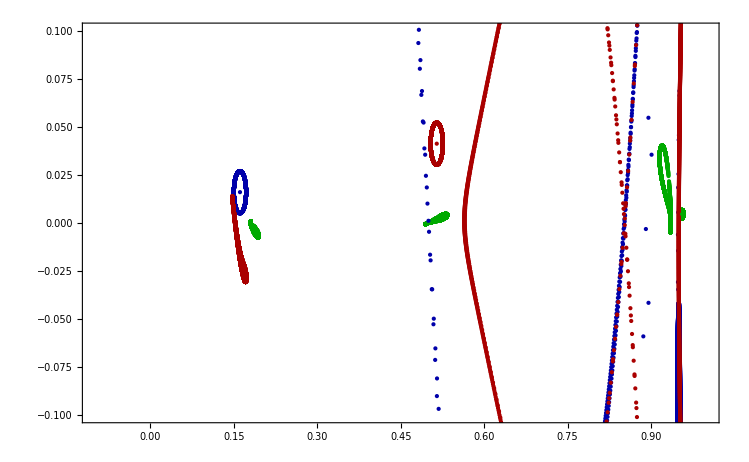

```mathematica
mu38=Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{-0.1,1},{-0.1,0.1}}]
```

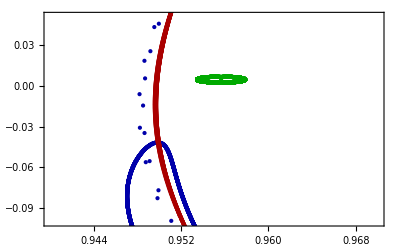

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.94,0.97},{-0.1,0.051}}]
```

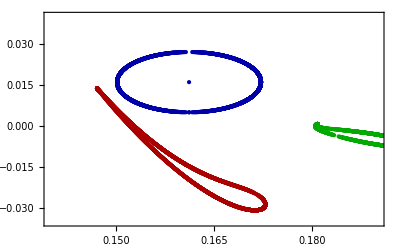

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.14,0.19},{-0.035,0.04}}]
```

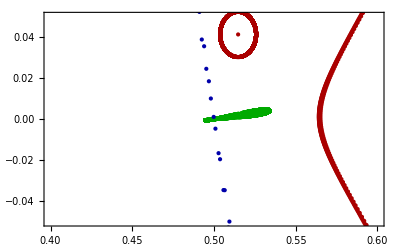

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Green]}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Darker[Red]}],Graphics[{Darker[Blue],PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],Graphics[{Darker[Red],PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],Graphics[{Darker[Green],PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}],PlotRange-> {{0.4,0.6},{-0.05,0.05}}]
```

```mathematica
Length[groupE]
groupE⟦98⟧
```

165

{3.823,0.956189,0.00198292}

16000

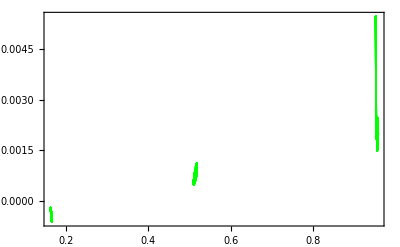

```mathematica
Block[{μ = groupE⟦98,1⟧},
list1 = {};
For[j=-1,j<1,j=j+0.001,
x=groupE⟦98,2⟧+10^-3 √(1-j^2)1/2;
y=groupE⟦98,3⟧+10^-3(j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupE⟦98,2⟧-10^-3 √(1-j^2)1/2;
y=groupE⟦98,3⟧+10^-3(j 1/2);
AppendTo[list1,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list1,{x, y}],i=5]
]
]
];
Length[list1]
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->{Green}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> All]
```

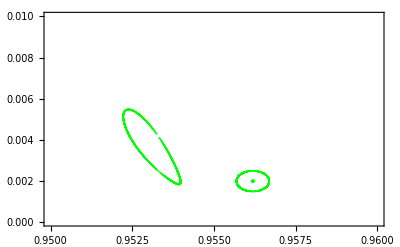

```mathematica
Show[ListPlot[list1,Frame->True,Joined->False,PlotStyle->{Green}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.95,0.96},{0,0.01}}]
```

```mathematica
N[groupE⟦98,1⟧-groupB⟦137,1⟧,20]
```

0.

```mathematica
groupB⟦137,1⟧
```

3.823

```mathematica
Block[{μ = groupB⟦137,1⟧},
list2 = {};
For[j=-1,j<1,j=j+0.001,
x=groupB⟦137,2⟧+10^-2 √(1-j^2)1/2;
y=groupB⟦137,3⟧+10^-2(j 1/2);
AppendTo[list2,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^3,AppendTo[list2,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupB⟦137,2⟧-10^-2 √(1-j^2)1/2;
y=groupB⟦137,3⟧+10^-2(j 1/2);
AppendTo[list2,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^3,AppendTo[list2,{x, y}],i=5]
]
]
];
Length[list2]
```

14806

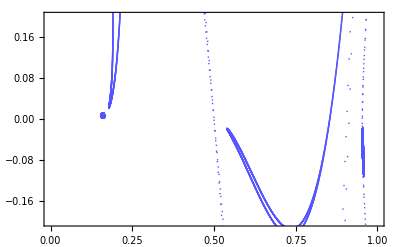

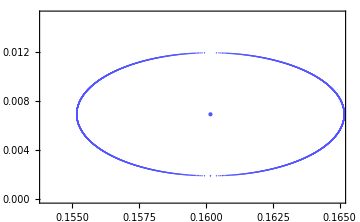

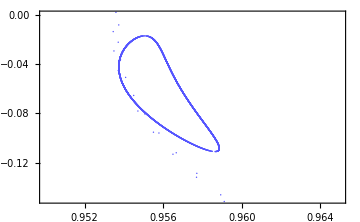

```mathematica
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Lighter[Blue]],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],PlotRange-> {{0,1},{-0.2,0.2}}]
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Lighter[Blue]],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],PlotRange-> {{0.154,0.165},{0,0.015}},ImageSize-> Medium]
Show[ListPlot[list2,Frame->True,Joined->False,PlotStyle->Lighter[Blue]],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],PlotRange-> {{0.95,0.965},{-0.15,0}},ImageSize-> Medium]
```

```mathematica
groupB⟦137,1⟧
```

3.823

```mathematica
N[groupB⟦137,1⟧-groupC⟦136,1⟧,20]
```

0.

16000

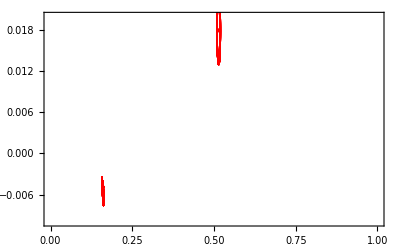

```mathematica
Block[{μ = groupC⟦136,1⟧},
list3 = {};
For[j=-1,j<1,j=j+0.001,
x=groupC⟦136,2⟧+10^-2 √(1-j^2)1/2;
y=groupC⟦136,3⟧+10^-2(j 1/2);
AppendTo[list3,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
];
For[j=-1,j<1,j=j+0.001,
x=groupC⟦136,2⟧-10^-2 √(1-j^2)1/2;
y=groupC⟦136,3⟧+10^-2(j 1/2);
AppendTo[list3,{x, y}];
For[i=1,i<4,i++,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[x^2+y^2≤ 10^1,AppendTo[list3,{x, y}],i=5]
]
]
];
Length[list3]
Show[ListPlot[list3,Frame->True,Joined->False,PlotStyle->Red],Graphics[{Red,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],PlotRange-> {{0,1},{-0.01,0.02}}]
```

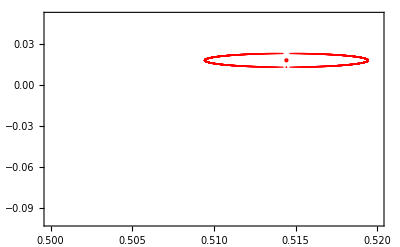

```mathematica
Show[ListPlot[list3,Frame->True,Joined->False,PlotStyle->Red],Graphics[{Red,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],PlotRange-> {{0.5,0.52},{-0.1,0.05}}]
```

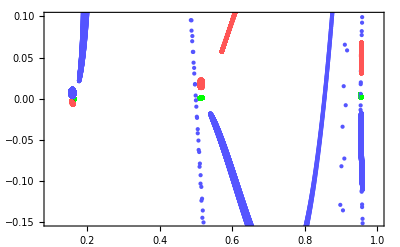

```mathematica
mu38233=Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.1,1},{-0.15,0.1}}]
```

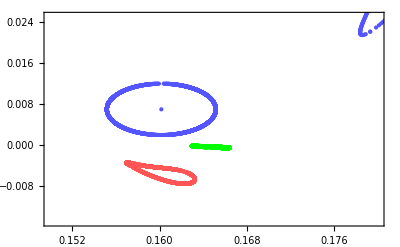

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.15,0.18},{-0.015,0.025}}]
```

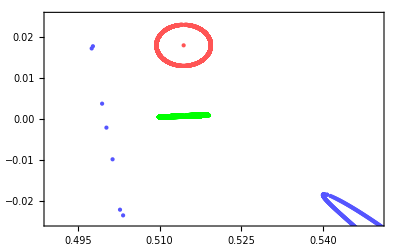

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],
PlotRange-> {{0.49,0.55},{-0.025,0.025}}]
```

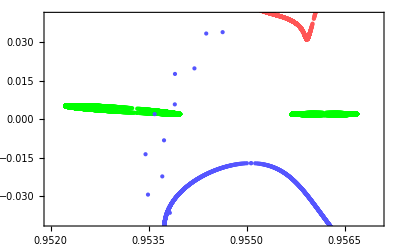

```mathematica
Show[
ListPlot[list1,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Green}],ListPlot[list2,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Blue]}],ListPlot[list3,Frame->True,Joined->False,PlotStyle->{PointSize[Small],Lighter[Red]}],Graphics[{Lighter[Blue],PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],Graphics[{Lighter[Red],PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],PlotRange-> {{0.952,0.957},{-0.04,0.04}}]
```

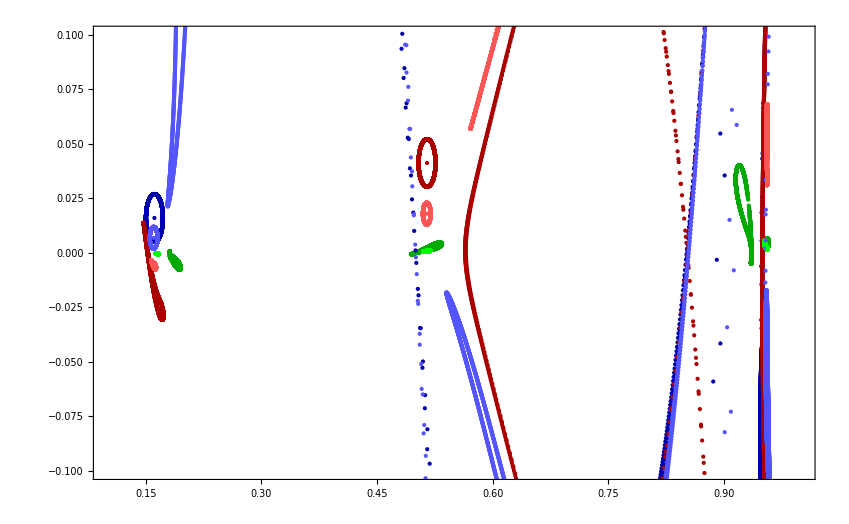

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.1,1},{-0.1,0.1}}]
```

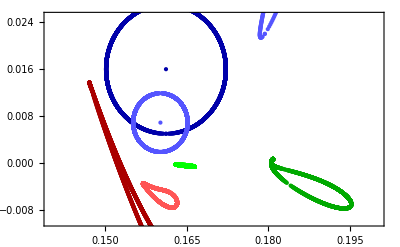

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.14,0.2},{-0.01,0.025}}]
```

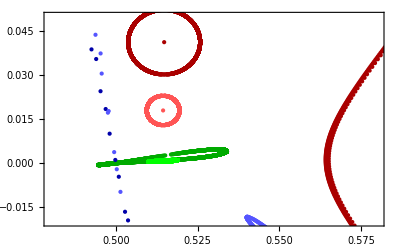

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.48,0.58},{-0.02,0.05}}]
```

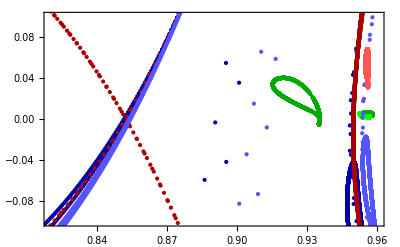

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.82,0.96},{-0.1,0.1}}]
```

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.9,0.96},{-0.05,0.05}}]
```

-Graphics-

```mathematica
Show[mu38,mu38233,PlotRange-> {{0.945,0.96},{-0.1,0.01}}]
```

-Graphics-

{{0.473404,0.00198292,3.823},{0.594309,0.00198292,3.823},{0.772079,0.00198292,3.823},{0.940895,0.00198292,3.823},{1.10971,0.00198292,3.823},{1.28748,0.00198292,3.823},{1.40839,0.00198292,3.823},{0.0405984,0.0179714,3.823},{0.154586,0.0179714,3.823},{0.329991,0.0179714,3.823},{0.500326,0.0179714,3.823},{0.670661,0.0179714,3.823},{0.846065,0.0179714,3.823},{0.960053,0.0179714,3.823},{-0.312971,0.00691646,3.823},{-0.198983,0.00691646,3.823},{-0.0235787,0.00691646,3.823},{0.146756,0.00691646,3.823},{0.317091,0.00691646,3.823},{0.492495,0.00691646,3.823},{0.606483,0.00691646,3.823}}

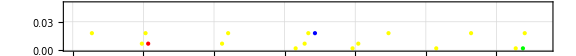

```mathematica
Clear[x,y]
subs1=NSolve[imaginary== 0/. {x-> groupE⟦98,2⟧+α,y-> groupE⟦98,3⟧,μ-> groupE⟦98,1⟧},α,Reals,Method->"EndomorphismMatrix"]⟦All,1,2⟧;
lista1=Table[{groupE⟦1,2⟧+α,groupE⟦98,3⟧,groupE⟦98,1⟧}/.α->subs⟦j⟧,{j,1,Length[subs]}];
subs2=NSolve[imaginary== 0/. {x-> groupC⟦136,2⟧+α,y-> groupC⟦136,3⟧,μ-> groupC⟦136,1⟧},α,Reals,Method->"EndomorphismMatrix"]⟦All,1,2⟧;
lista2=Table[{groupC⟦1,2⟧+α,groupC⟦136,3⟧,groupC⟦136,1⟧}/.α->subs2⟦j⟧,{j,1,Length[subs]}];
subs3=NSolve[imaginary== 0/. {x-> groupB⟦137,2⟧+α,y-> groupB⟦137,3⟧,μ-> groupB⟦137,1⟧},α,Reals,Method->"EndomorphismMatrix"]⟦All,1,2⟧;
lista3=Table[{groupB⟦1,2⟧+α,groupB⟦137,3⟧,groupB⟦137,1⟧}/.α->subs2⟦j⟧,{j,1,Length[subs]}];
lista=Join[lista1,lista2,lista3]
p2=Show[
Graphics[{Green,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],Graphics[{Red,PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],Graphics[{Blue,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],Table[Graphics[{Yellow,PointSize[Medium],Point[lista⟦j,1;;2⟧]}],{j,1,Length[lista]}],PlotRange-> {{0,1},{0,0.05}},Frame-> True,GridLines-> Automatic,AspectRatio-> 1/10,ImageSize-> Large]
```

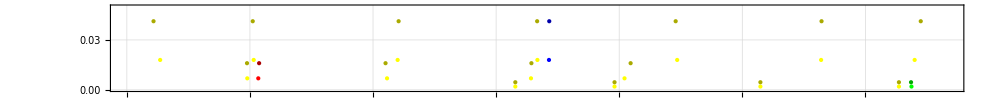

```mathematica
Show[p2,p1]
```

```mathematica
subs1=NSolve[imaginary== 0/. {x-> groupE⟦98,2⟧+α,y-> groupE⟦98,3⟧,μ-> groupE⟦98,1⟧},α,Reals,Method->"EndomorphismMatrix"]⟦All,1,2⟧
```

{-0.913954,-0.801466,-0.626188,-0.456189,-0.286189,-0.110911,0.00157686}

```mathematica
ContourPlot[imaginary /. μ-> groupE⟦1,1⟧,{x,0,1},{y,0,0.02},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
ContourPlot[imaginary /. μ-> groupE⟦98,1⟧,{x,0,1},{y,0,0.02},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
Show[
ContourPlot[imaginary /. μ-> groupE⟦98,1⟧,{x,0.1,1},{y,0,0.02},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}]]
```

-Graphics-

```mathematica
GraphicsRow[{Show[
ContourPlot[imaginary /. μ-> groupE⟦1,1⟧,{x,0.15,0.165},{y,0,0.05},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}]],
Show[
ContourPlot[imaginary /. μ-> groupE⟦98,1⟧,{x,0.15,0.165},{y,0,0.05},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}]]}]
```

-Graphics-

```mathematica
GraphicsRow[{Show[
ContourPlot[imaginary /. μ-> groupE⟦1,1⟧,{x,0.45,0.55},{y,0.01,0.05},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}]],
Show[
ContourPlot[imaginary /. μ-> groupE⟦98,1⟧,{x,0.45,0.55},{y,0.01,0.05},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}]]}]
```

-Graphics-

```mathematica
GraphicsRow[{Show[
ContourPlot[imaginary /. μ-> groupE⟦1,1⟧,{x,0.95,0.96},{y,0,0.02},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦1,2⟧,groupB⟦1,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦1,2⟧,groupC⟦1,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦1,2⟧,groupE⟦1,3⟧}]}]],Show[
ContourPlot[imaginary /. μ-> groupE⟦98,1⟧,{x,0.95,0.96},{y,0,0.02},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}]]}]
```

-Graphics-

```mathematica
Show[
ContourPlot[imaginary /. μ-> groupE⟦98,1⟧,{x,0.9575,0.96},{y,0,0.01},ContourLabels->True,MaxRecursion->3,PerformanceGoal->"Quality"],
Graphics[{Red,PointSize[Large],Point[{groupB⟦137,2⟧,groupB⟦137,3⟧}]}],
Graphics[{Green,PointSize[Large],Point[{groupC⟦136,2⟧,groupC⟦136,3⟧}]}],
Graphics[{Blue,PointSize[Large],Point[{groupE⟦98,2⟧,groupE⟦98,3⟧}]}],GridLines-> Automatic]
```

-Graphics-

```mathematica
imaginary/.{ μ-> groupE⟦98,1⟧,x-> 0.9580,y-> 0.0065}
```

6.2136×10^-6

```mathematica
Clear[x,y]
```

```mathematica
re1=FullSimplify[Normal[Series[real,{y,0,1}]]]
im1=FullSimplify[Normal[Series[imaginary,{y,0,1}]]]
```

(-1+x) x μ^3 (-1+(-1+x) x μ (-1-μ (1+(-1+x) x μ)^2))

-(-1+2 x) y μ^3 (1+2 (-1+x) x μ (1+μ+3 (-1+x) x μ^2+2 (-1+x)^2 x^2 μ^3))

```mathematica
Block[{μ = groupE⟦120,1⟧},
listpointsxy = {};

For[j=2,j<100,j++,
x =(j-1)10^-2;
For[k=-1,k≤ 1,k++,
y = k 10^-2;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
For[i=1,i<100,i++,
If[x^2+y^2≤ 1,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α  y,0}],
i=100]
]
]
];

Length[listpointsxy];

(*pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];*)
p3828D=Show[Plot3D[Re[D[map3[xx,y,μ]-xx,{xx,1}]]/. xx-> x,{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Large,ViewPoint->{0,0,3}]
]
```

-Graphics3D-

```mathematica
Block[{μ = 3.8},
listpointsxy = {};

For[j=2,j< 4 10^3,j++,
x =(j-1)1/(4 10^3);
For[k=-1,k≤ 1,k++,
y = k 10^-2;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
For[i=1,i<100,i++,
If[x^2+y^2≤ 1,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α  y,0}],
i=100]
]
]
];

Length[listpointsxy];

(*pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];*)
p38D=Show[Plot3D[Re[D[map3[xx,y,μ]-xx,{xx,1}]]/. xx-> x,{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Large,ViewPoint->{0,0,Infinity}]
]
```

$Aborted

```mathematica
Show[p3828D,PlotRange-> {{0.45,0.55},{-0.01,0.01},{-0.1,0.1}}]
```

-Graphics3D-

```mathematica
Show[p38D,PlotRange-> {{0.45,0.55},{-0.01,0.01},{-0.1,0.1}}]
```

-Graphics3D-

```mathematica
Plot3D[Re[map3[xx,y,3.8]-map3[xx,y,3.828]]/. xx-> x,{x,0,1},{y,-0.15,0.15},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}]
```

-Graphics3D-

```mathematica
Show[Plot3D[Re[D[map3[xx,y,3.8]-xx,{xx,1}]]/. xx-> x,{x,0.1,0.3},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
Show[Plot3D[Re[D[map3[xx,y,3.828]-xx,{xx,1}]]/. xx-> x,{x,0.1,0.3},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6],}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
groupB⟦117,1⟧
```

3.82033

```mathematica
Block[{μ = groupB⟦117,1⟧},
listpointsxy = {};

For[j=2,j≤ 4 10^2,j++,
x =(j-1)1/(4 10^2);
For[k=-4,k≤ 4,k=K+0.3,
y = k 10^-3;
AppendTo[listpointsxy,{x,y,0}];
For[i=1,i≤ 10,i++,
If[x^2+y^2≤ 2,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x, y,0}],
i=100]
]
]
];

Length[listpointsxy];

pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];
pr=Show[Plot3D[Re[map3[xx,y,μ]-xx]/. xx-> x,{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]},MeshFunctions->{#3&},Mesh->5],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}];
pi=Show[Plot3D[Im[map3[x,y,μ]]-y,{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]},MeshFunctions->{#3&},Mesh->5],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}];
]
```

```mathematica
groupB⟦117,1⟧
```

3.82033

```mathematica
groupC⟦117,1⟧
```

3.82033

```mathematica
groupE⟦92,1⟧
```

3.82033

```mathematica
Show[pr,Graphics3D[{Black,PointSize[0.05],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧,0}]}],Graphics3D[{Black,PointSize[0.05],Point[{groupC⟦117,2⟧,groupC⟦117,3⟧,0}]}],Graphics3D[{Black,PointSize[0.05],Point[{groupE⟦92,2⟧,groupE⟦92,3⟧,0}]}]]
```

-Graphics3D-

```mathematica
Show[Plot3D[Re[map3[xx,y,groupB⟦117,1⟧]-xx]/. xx-> x,{x,0.13,0.2},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]},MeshFunctions->{#3&},Mesh->5],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],Graphics3D[{Black,PointSize[0.05],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧,0}]}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
Show[Plot3D[Re[map3[xx,y,groupC⟦117,1⟧]-xx]/. xx-> x,{x,0.45,0.55},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]},MeshFunctions->{#3&},Mesh->5],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],Graphics3D[{Black,PointSize[0.05],Point[{groupC⟦117,2⟧,groupC⟦117,3⟧,0}]}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
Show[Plot3D[Re[map3[xx,y,groupE⟦117,1⟧]-xx]/. xx-> x,{x,0.95,0.96},{y,-0.02,0.02},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]},MeshFunctions->{#3&},Mesh->5],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],Graphics3D[{Black,PointSize[0.05],Point[{groupE⟦117,2⟧,groupE⟦117,3⟧,0}]}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
Show[Plot3D[Re[map3[xx,y,groupB⟦117,1⟧]-xx]/. xx-> x,{x,0.1,0.3},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]},MeshFunctions->{#3&},Mesh->5],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],Graphics3D[{Lighter[Blue],PointSize[Large],Point[{groupB⟦117,2⟧,groupB⟦117,3⟧,0}]}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
```

```mathematica
map3[x,y,3.8]-y/. {x-> 0.2, y-> 10^-2}
```

-1.40803×10^8-1.39624×10^6 ⅈ

```mathematica
Block[{μ = 3.8280},
listpointsxy = {};

For[j=2,j<200,j++,
x =(j-1)10^-2/2;
For[k=-1,k≤ 1,k++,
y = k 10^-2;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
For[i=1,i<10,i++,
If[x^2+y^2≤ 1,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α  y,0}],
i=100]
]
]
];

Length[listpointsxy];

pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];
Show[Plot3D[Re[D[map3[xx,y,μ]-xx,{xx,1}]]/. xx-> x,{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Medium,ViewPoint->{0,0,Infinity}]
]
```

-Graphics3D-

```mathematica
Block[{μ = 3.82845},
listpointsxy = {};

For[j=2,j<200,j++,
x =(j-1)10^-2/2;
For[k=-1,k≤ 1,k++,
y = k 10^-2;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
For[i=1,i<10,i++,
If[x^2+y^2≤ 1,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α  y,0}],
i=100]
]
]
];

Length[listpointsxy];

pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];
Show[Plot3D[Im[D[map3[x,yy,μ]-yy,{yy,1}]]/. yy-> y,{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Large,ViewPoint->{0,0,Infinity}]
]
```

-Graphics3D-

```mathematica
Block[{μ = 3.82845},
listpointsxy = {};

For[j=2,j<200,j++,
x =(j-1)10^-2/2;
For[k=-1,k≤ 1,k++,
y = k 10^-2;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
For[i=1,i<10,i++,
If[x^2+y^2≤ 1,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α  y,0}],
i=100]
]
]
];

Length[listpointsxy];

pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];
Show[Plot3D[Re[map3[x,y,μ]-x],{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Large,ViewPoint->{0,0,Infinity}]
]
```

-Graphics3D-

```mathematica
Show[pts,PlotRange-> {{0,1},{-100,100},Automatic}]
```

```mathematica
Plot3D[{x,Re[map3[x,y,3.826]]},{x,0.15,0.18},{y,-0.04,0.04}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[{x,Re[map3[x,y,μ]]},{x,0.1,0.2},{y,-0.04,0.04},PlotRange->{0.1,0.3}],{μ,3.8,3.8285,0.0001}]
```

```mathematica
Plot3D[{Im[map3[x,y,3.8]],y},{x,0,1},{y,-0.04,0.04},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot[thelistf⟦1,2⟧[μ],{μ,3.8,3.8284}]
```

```mathematica
Block[{μ = 3.82},
listpointsxμ = {};

For[j=2,j< 3 10^2,j++,
x =(j-1)1/(3 10^2);
For[k=-1,k≤ 1,k++,
y = k 10^-1;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
For[i=1,i<100,i++,
If[x^2+y^2≤ 1,
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
If[y^2<10^-6,
AppendTo[listpointsxμ,{x}],
Null],
i=100]
]
]
];

Length[listpointsxμ];
(*pts=Show[ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Large}],ListPointPlot3D[listpointsxy,PlotStyle->Red]/.Point[a___]:>{Thick,Line[a]},PlotRange->{{0,1},{-0.1,0.1},Automatic}];*)
(*p38D=Show[Plot3D[Re[D[map3[xx,y,μ]-xx,{xx,1}]]/. xx-> x,{x,0,1},{y,-0.1,0.1},PlotRange->Automatic,ColorFunction->Function[{x,y,z},Hue[z]],PlotStyle-> {Opacity[0.6]}],ListPointPlot3D[listpointsxy,PlotStyle->{Red,PointSize-> Medium}],ImageSize-> Large,ViewPoint->{0,0,Infinity}]*)
]
```

```mathematica
ListPlot[listpointsxμ,PlotRange->{0,1},Frame->True]
```

-Graphics-

```mathematica
ListPlot[Flatten[listpointsxμ]]
```

-Graphics-

```mathematica
Histogram[{Flatten[listpointsxμ]},{5 10^-3}]
```

-Graphics-

```mathematica
listpointsxμ
```

{{0.814909},{0.932832},{0.695473},{0.590171},{0.268449},{0.715892},{0.661995},{0.474252},{0.172943},{0.946779},{0.593755},{0.27658},{0.688119},{0.564283},3566,{0.929252},{0.718418},{0.670798},{0.504104},{0.164388},{0.952663},{0.544698},{0.190472},{0.924732},{0.745623},{0.762409},{0.814236},{0.931881},{0.701692}}
 |  |  |  |

```mathematica
listpointsxμT = {}
(* valores de mu na lista total*)
For[μ = 3.8, μ<3.835,μ=μ+0.01;
listpointsxμlocal = {};
(* valores de 0 a 1 a serem testados para x*)

For[j=2,j< 3 10^2,j++,
x =(j-1)1/(3 10^2);
(* ? *)
For[k=-1,k≤ 1,k++,
y = k 10^-1;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
(* definicao do n de iteracoes *)
For[i=1,i<100,i++,
(* condicao de estabilidade *)
If[x^2+y^2≤ 1,
(* processo de iteracao *)
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
(* condicao para reduzir valores *)
If[y^2<10^-4,
(* adicao dos valores de x para um unico mu a uma lista *)
AppendTo[listpointsxμlocal,{x}],
Null],
i=100]]]];
(* adicao das listas contendo os valores de x para diferentes mu's em uma unica lista *)
AppendTo[listpointsxμT, listpointsxμlocal]]
```

{}

```mathematica
Length[listpointsxμT]
```

4

```mathematica
listpointsxμT⟦2⟧
```

{{0.814909},{0.932832},{0.695473},{0.590171},{0.268449},{0.715892},{0.661995},{0.474252},{0.172943},{0.946779},{0.593755},{0.27658},{0.688119},{0.564283},3568,{0.81139},{0.927661},{0.728218},{0.704572},{0.622261},{0.350202},{0.434071},{0.220831},{0.860497},{0.94844},{0.580287},{0.247446},{0.859334},{0.949414}}
 |  |  |  |

```mathematica
Histogram[{Flatten[listpointsxμT⟦2⟧]},{5 10^-3}]
```

-Graphics-

```mathematica
Histogram[{Flatten[listpointsxμT⟦3⟧]},{5 10^-3}]
```

-Graphics-

```mathematica
listpointsxμT = {}
(* valores de mu na lista total*)
For[μ = 3.8, μ<3.8284,μ=μ+0.001;
listpointsxμlocal = {};
(* valores de 0 a 1 a serem testados para x*)

For[j=2,j< 3 10^2,j++,
x =(j-1)1/(3 10^2);
(* ? *)
For[k=-1,k≤ 1,k++,
y = k 10^-1;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
(* definicao do n de iteracoes *)
For[i=1,i<100,i++,
(* condicao de estabilidade *)
If[x^2+y^2≤ 1,
(* processo de iteracao *)
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
(* condicao para reduzir valores *)
If[y^2<10^-6,
(* adicao dos valores de x para um unico mu a uma lista *)
AppendTo[listpointsxμlocal,{x}],
Null],
i=100]]]];
(* adicao das listas contendo os valores de x para diferentes mu's em uma unica lista *)
AppendTo[listpointsxμT, listpointsxμlocal]]
```

{}

```mathematica
Manipulate[Histogram[{Flatten[listpointsxμT⟦t⟧]},{5 10^-2}],{t,1,100}]
```

Part::pkspec1: The expression 13.2 cannot be used as a part specification.

Part::pkspec1: The expression 25.4 cannot be used as a part specification.

Part::pkspec1: The expression 37.6 cannot be used as a part specification.

Part::pkspec1: The expression 56.5 cannot be used as a part specification.

Part::pkspec1: The expression 69.1 cannot be used as a part specification.

```mathematica
listpointsxμT = {}
(* valores de mu na lista total*)
For[μ = 3.8, μ<3.8284,μ=μ+0.001;
listpointsxμlocal = {};
x = 0.5;
y = 10^-5;
AppendTo[listpointsxy,{x,α y,0}];
(* definicao do n de iteracoes *)
For[i=1,i<101,i++,
(* condicao de estabilidade *)
If[x^2+y^2≤ 1,
(* processo de iteracao *)
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
(* condicao para reduzir valores *)
If[y^2<10^-2,
(* adicao dos valores de x para um unico mu a uma lista *)
AppendTo[listpointsxμlocal,x],
Null],
i=100]];
(* adicao das listas contendo os valores de x para diferentes mu's em uma unica lista *)
AppendTo[listpointsxμT, listpointsxμlocal]]
```

{}

```mathematica
Length[listpointsxy]
```

351361

```mathematica
ListPlot[listpointsxy]
```

```mathematica
Length[listpointsxμT]
```

29

```mathematica
Table[Histogram[{Flatten[listpointsxμT⟦i⟧]},{5 10^-2}], {i,1,29}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 2 of {Missing[]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[listpointsxμT]
```

29